## Week 1 – Stanford Machine Learning

### Linear Regression

Let us create some random data, say housing sizes in square feet on x and price levels on y, and plot it.

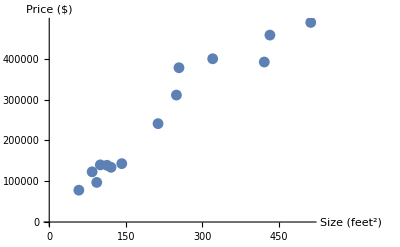

```mathematica
trainX={100,320,213,512,58,84,113,142,93,121,421,432,249,254};
trainY={140000,400000,241000,489000,78000,123000,139000,143000,97000,134000,392000,458000,311000,378000};
trainComposed=Transpose@{trainY,Table[1,{Length[trainX]}],trainX};
listPlot=ListPlot[Transpose@{trainX,trainY},AxesLabel->{"Size (feet^2)","Price ($)"}];
Show[listPlot]
```

Now, we define a linear hypothesis function since our data seems to allow for a linear approximation

```mathematica
Hyp[x_,θ_]:=θ.x;
```

followed by the squared error cost function

```mathematica
Cost[θ_]:=1/2 Total[(Hyp[{##2},θ]-#1)^2&@@@trainComposed];
```

We then minimise the cost function, after which we plot the hypothesis function with the minimised values

{10105881123250000/998147,{v[1]→38758111500/998147,v[2]→955610000/998147}}

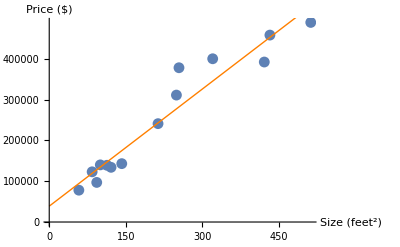

```mathematica
Clear[v]
θ=Array[v,Length[trainComposed[[1]]]-1];
regression=Minimize[Cost[θ],θ]
regressionPlot:=Plot[Hyp[{1,x},{v[1],v[2]}/.regression[[2]]],{x,0,Max[trainX]},PlotStyle->{Orange,Thin}]
Show[listPlot,regressionPlot]
```

### Gradient Descent

Let us repeat the regression analysis by using gradient descent instead, using the same data. First, we create the step function that returns the next step of the gradient descent algorithm using the update rule. Note that because of the huge values on the pricing axis, the learning rate parameters are particularly sensitive. Any learning rate above 1 10^-7 will thus make the gradient descent algorithm overshoot. Instead of setting a very low learning rate parameter, as below, a better fix would be to represent the housing prices in terms of thousand dollars.

```mathematica
Clear[v]
α={0.1,0.0000003};
θ=Array[v,Length[trainComposed[[1]]]-1];
Step[θ_]:=θ+α Sum[(trainY[[i]]-Hyp[trainComposed[[i,2;;]],θ])trainComposed[[i,2;;]],{i,1,Length[trainX]}]
```

To see how we actually learn, we can make a contour plot of the cost function and of the results as we step through.

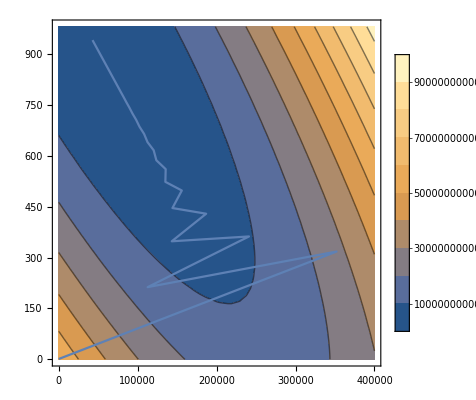

```mathematica
contourPlot:=ContourPlot[Cost[{x,y}],{x,0,400000},{y,0,980},PlotLegends->Automatic];
gradientDescentPlot:=ListLinePlot[NestList[Step,{1,1},50],AxesLabel->{"x","y"},PlotStyle->{}]
Show[contourPlot,gradientDescentPlot]
```

Moreover, we can plot the step function as a function of the iterations to picture the learning rate. We do so by creating the learning function

```mathematica
Learning[x_]:=Cost@Nest[Step,{1,1},x];
```

We do indeed learn, as seen in the plot below

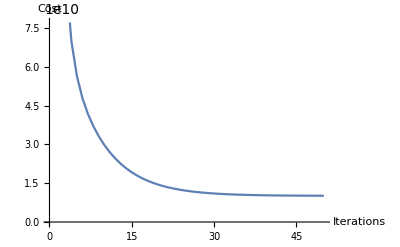

```mathematica
learningRate=ListLinePlot[#,AxesLabel->{"Iterations","Cost"}]&@Transpose@{Range[0,50],Learning/@Range[0,50]}
```

We then step through the algorithm fifty times and plot all the lines of all intermediate steps to see how the regression converges towards the optimum

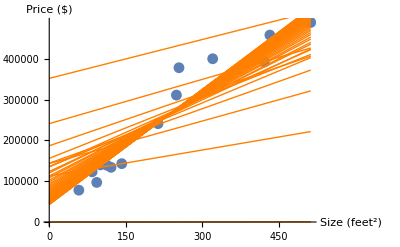

```mathematica
gradientDescentRegressionPlot=Show[Plot[Hyp[{1,x},#],{x,0,Max[trainX]},PlotStyle->{Orange,Thin}]&/@(Nest[Step,{1,1},#]&/@Range[0,50])];
Show[listPlot,gradientDescentRegressionPlot]
```

### Linear Regression using the Normal Equations

For data that only contains a small set of features we can easilier find the optimum by using the normal equations. Note that since these equations need to find the inverse, if the feature matrix is particularly large, it is better to use the gradient descent algorithm since finding the inverse is an O(n^3) operation. 

We prepare our data set

```mathematica
X=Transpose@{Table[1,{Length[trainX]}],trainX};
Y=trainY;
```

and find the optimal parameters

```mathematica
θ=Inverse[Transpose[X].X].Transpose[X].trainY;
```

Lastly, we plot the parameters to show that it is indeed the optimum.

```mathematica
normalEquationPlot=Plot[Hyp[{1,x},θ],{x,0,Max[trainX]},PlotStyle->{Orange,Thin}];
Show[listPlot,normalEquationPlot]
```

-Graphics-